{{x→InterpolatingFunction[{{0., 1000.}}, <>],y→InterpolatingFunction[{{0., 1000.}}, <>]}}

```mathematica
gNa := 0.5
gK := 0.5 
gL := 0.5
mInf := 0.7
nInf := 2
eNa := 1
eK := 1 
eL := 1
```

```mathematica
tauN := 2
```

```mathematica
V_div := -gNa*mInf^3(1-nn[t])(V[t]-eNa)-gK * nn[t]^4(V[t]-eK)-gL(V[t]-eL)
n_div :=(nInf-nn[t])/(tauN)
```

Unset::write: Tag Function in (0&)[t] is Protected.

Unset::norep: Assignment on V for V[t] not found.

```mathematica
fastSlow=NDSolve[{V'[t]==-gNa*mInf^3(1-nn[t])(V[t]-eNa)-gK * nn[t]^4(V[t]-eK)-gL(V[t]-eL),nn'[t]==(nInf-nn[t])/(tauN),V[0]==nn[0]==1},{V, nn},{t,10}]
```

{{V→InterpolatingFunction[{{0., 10.}}, <>],nn→InterpolatingFunction[{{0., 10.}}, <>]}}

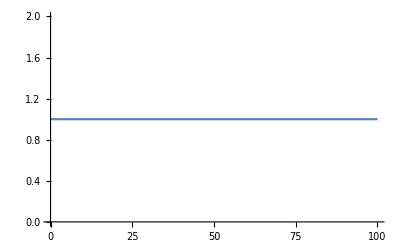

```mathematica
Plot[V[t]/.fastSlow,{t,0,100}]
```

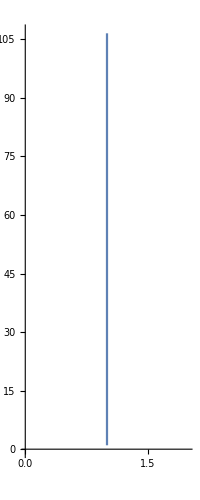

```mathematica
ParametricPlot[Evaluate[{V[t],nn[t]}/.fastSlow],{t,0,100}]
```